```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=500;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*tϕ=ts/200;
αϕ=α/200;*)
tϕ=0.4ts;
αϕ2=1.0 π;
θ1=0.5π;
θ2=0.0 π;
ϕ = 0.0 π;
```

```mathematica
H[ϕ_]:=Block[{htp},
ϵ0=2ts Cos[Pi/(Nx+1.0)];
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx/2,Nx/2}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx/2,Nx/2}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx/2,Nx/2}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx/2,Nx/2}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx/2,Nx/2}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx/2,Nx/2}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];




H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx/2,Nx/2}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx/2,Nx/2}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2 (Cos[αϕ2]+ⅈ Sin[αϕ2]),Band[{2,1}]->α/2(-Cos[αϕ2]+ⅈ Sin[αϕ2])},{Nx/2,Nx/2}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2(- Cos[αϕ2]-ⅈ Sin[αϕ2]),Band[{2,1}]->α/2(Cos[αϕ2]-ⅈ Sin[αϕ2])},{Nx/2,Nx/2}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx/2,Nx/2}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx/2,Nx/2}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

H12=SparseArray[{{Nx/2,1}->tϕ,{2Nx/2,Nx/2+1}->tϕ,{3Nx/2,2Nx/2+1}->-tϕ,{4Nx/2,3Nx/2+1}->-tϕ},{4Nx/2,4Nx/2}];
H21=Conjugate[Transpose[H12]];

htp=SparseArray[ArrayFlatten[{{H11,H12},{H21,H22}}]];

htp
];
```

```mathematica
{e0,ψ0}=Transpose[Sort[Transpose[Eigensystem[H[0.0],-10]]]];
```

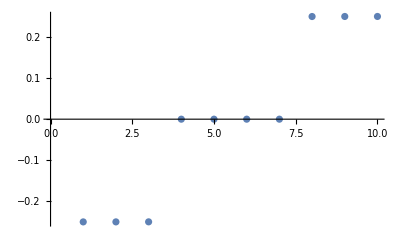

```mathematica
ListPlot[e0]
```

```mathematica
nt=6;
Pl=Join[Table[Abs[ψ[[nt,i]]]^2,{i,1,Nx/2}],Table[Abs[ψ[[nt,i]]]^2,{i,2Nx+1,2Nx+Nx/2}]];
```

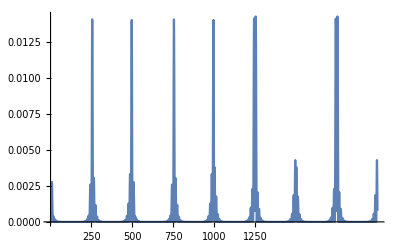

```mathematica
ListPlot[Abs[ψ0[[nt]]]^2,Ticks->{{Nx/2, Nx,3/2Nx,2Nx,2Nx+Nx/2}, Automatic},Joined->True,PlotRange->All]
```

```mathematica
nt=6;
Pl=Join[Table[Abs[ψ0[[nt,i]]]^2,{i,1,Nx/2}],Table[Abs[ψ0[[nt,i]]]^2,{i,2Nx+1,2Nx+Nx/2}]];
Pl2=Join[Table[Abs[ψ0[[nt+1,i]]]^2,{i,1,Nx/2}],Table[Abs[ψ0[[nt+1,i]]]^2,{i,2Nx+1,2Nx+Nx/2}]];
```

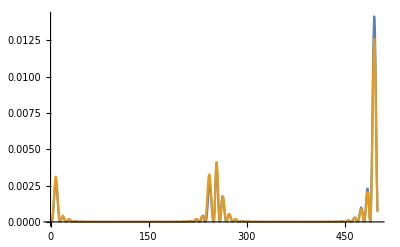

```mathematica
ListPlot[{Pl,Pl2},Joined->True,PlotRange->All]
```

```mathematica
a=SessionTime[];
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,

Hsp = H[ϕ];



etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];

b=SessionTime[];
Print[{ϕ,b-a}];
];
```

{0,0.0927326}

{0.1,0.185485}

{0.2,0.273251}

{0.3,0.343064}

{0.4,0.422852}

{0.5,0.492225}

{0.6,0.564034}

{0.7,0.635355}

{0.8,0.706678}

{0.9,0.775007}

{1.,0.8498081}

{1.1,0.9236101}

{1.2,0.9954282}

{1.3,1.072213}

{1.4,1.143028}

{1.5,1.226799}

{1.6,1.303595}

{1.7,1.377399}

{1.8,1.452197}

{1.9,1.527995}

{2.,1.599812}

{2.1,1.668618}

{2.2,1.742434}

{2.3,1.816103}

{2.4,1.893894}

{2.5,1.962709}

{2.6,2.031526}

{2.7,2.102336}

{2.8,2.173147}

{2.9,2.240965}

{3.,2.312785}

{3.1,2.379598}

{3.2,2.447414}

{3.3,2.514235}

{3.4,2.582053}

{3.5,2.651867}

{3.6,2.717692}

{3.7,2.784511}

{3.8,2.85632}

{3.9,2.923145}

{4.,2.988967}

{4.1,3.057781}

{4.2,3.126597}

{4.3,3.19442}

{4.4,3.26224}

{4.5,3.332051}

{4.6,3.399337}

{4.7,3.467158}

{4.8,3.538483}

{4.9,3.607812}

{5.,3.680616}

{5.1,3.752933}

{5.2,3.82275}

{5.3,3.890564}

{5.4,3.960378}

{5.5,4.03119}

{5.6,4.099006}

{5.7,4.167824}

{5.8,4.237637}

{5.9,4.30346}

{6.,4.373274}

{6.1,4.448075}

{6.2,4.514895}

{6.3,4.58471}

{6.4,4.653562}

{6.5,4.723375}

{6.6,4.791195}

{6.7,4.868985}

{6.8,4.937802}

{6.9,5.010126}

{7.,5.079939}

{7.1,5.152886}

{7.2,5.222236}

{7.3,5.297573}

{7.4,5.369344}

{7.5,5.440662}

{7.6,5.511484}

{7.7,5.581286}

{7.8,5.649106}

{7.9,5.718919}

{8.,5.792721}

{8.1,5.863532}

{8.2,5.938333}

{8.3,6.011139}

{8.4,6.082946}

{8.5,6.150763}

{8.6,6.217586}

{8.7,6.285404}

{8.8,6.35074}

{8.9,6.417076}

{9.,6.480905}

{9.1,6.549722}

{9.2,6.616542}

{9.3,6.682366}

{9.4,6.746195}

{9.5,6.814014}

{9.6,6.879837}

{9.7,6.947168}

{9.8,7.012507}

{9.9,7.0773337}

{10.,7.1416737}

{10.1,7.2080313}

{10.2,7.2778201}

{10.3,7.3456394}

{10.4,7.4104646}

{10.5,7.4792815}

{10.6,7.5490943}

{10.7,7.6149173}

{10.8,7.6827365}

{10.9,7.7505546}

{11.,7.8233626}

{11.1,7.8921773}

{11.2,7.9639867}

{11.3,8.035793}

{11.4,8.105607}

{11.5,8.17892}

{11.6,8.2477439}

{11.7,8.3155614}

{11.8,8.3833804}

{11.9,8.4651625}

{12.,8.5335858}

{12.1,8.601402}

{12.2,8.6690681}

{12.3,8.7393877}

{12.4,8.8092038}

{12.5,8.8775312}

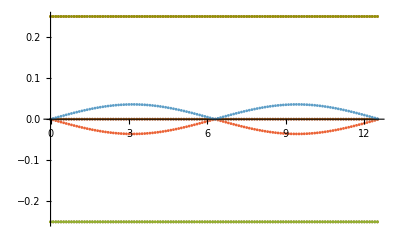

```mathematica
ListPlot[elϕ,PlotStyle->PointSize[0.005]]
```